```mathematica
Cat=ImageData[-Graphics-];
```

```mathematica
CatRed=Cat[[All,All,1]];
Dimensions[CatRed]
```

{500,730}

```mathematica
{251,370}
CatRed[[1,1]]
```

{251,370}

0.929412

```mathematica
SVDThreshold=50;
```

```mathematica
CatGreen=Cat[[All,All,2]];
```

```mathematica
CatBlue=Cat[[All,All,3]];
```

```mathematica
SVDCatRed=SingularValueDecomposition[CatRed,SVDThreshold];
```

```mathematica
SVDCatBlue=SingularValueDecomposition[CatBlue,SVDThreshold];
```

```mathematica
SVDCatGreen=SingularValueDecomposition[CatGreen,SVDThreshold];
Σ =SVDCatRed[[2]];
```

```mathematica
U=SVDCatRed[[1]];
```

```mathematica
VTr=Transpose[SVDCatRed[[3]]];
```

```mathematica
SVDCatRedMult=U.Σ .VTr;
```

```mathematica
Image[SVDCatRedMult]
```

-Graphics-

```mathematica
SingValuesRed=Diagonal[Σ];
```

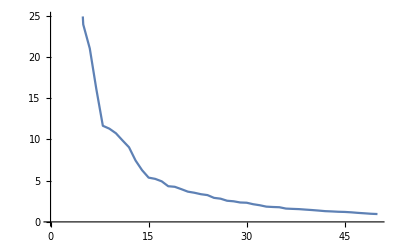

```mathematica
ListLinePlot[SingValuesRed]
```

```mathematica
ΣBlue =SVDCatBlue[[2]];
```

```mathematica
UBlue=SVDCatBlue[[1]];
```

```mathematica
VTrBlue=Transpose[SVDCatBlue[[3]]];

SVDCatBlueMult=UBlue.ΣBlue .VTrBlue;
```

```mathematica
Image[SVDCatBlueMult]
```

-Graphics-

```mathematica
SingValuesBlue=Diagonal[ΣBlue];
```

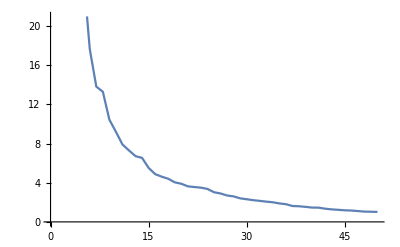

```mathematica
ListLinePlot[SingValuesBlue]
```

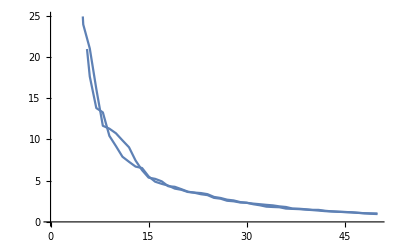

```mathematica
Show[ListLinePlot[SingValuesRed],ListLinePlot[SingValuesBlue]]
```

```mathematica
ΣGreen =SVDCatGreen[[2]];
UGreen=SVDCatGreen[[1]];
```

```mathematica
VTrGreen=Transpose[SVDCatGreen[[3]]];
```

```mathematica
SVDCatGreenMult=UGreen.ΣGreen .VTrGreen;
SingValuesGreen=Diagonal[ΣGreen];
```

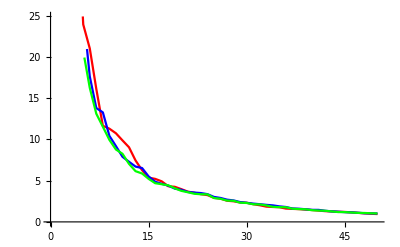

```mathematica
Show[ListLinePlot[SingValuesRed,PlotStyle->Red],ListLinePlot[SingValuesBlue,PlotStyle->Blue],ListLinePlot[SingValuesGreen,PlotStyle->Green]]
```

```mathematica
Image[SVDCatGreenMult]
```

-Graphics-

```mathematica
dim=Dimensions[Cat];
m=dim[[1]];
n=dim[[2]];
FinalSVDCat=Table[0,{i,m},{j,n}];
For[i=1,i≤m,i++,
For[j=1,j≤n,j++,
r=SVDCatRedMult[[i,j]];
g=SVDCatGreenMult[[i,j]];
b=SVDCatBlueMult[[i,j]];
FinalSVDCat[[i,j]]={r,g,b};
]
]
```

```mathematica
Image[FinalSVDCat]
```

-Graphics-